```mathematica
(*We will now define our coefficients*)
```

```mathematica
k1= 2 ;(*This will be our spring constant or how responsive we are to the distance to the lead car*)
k2=3;(*This will be the friction constant or road conditions or how we are noticing the speed of the lead car *)
v = 5 ;(*This will be the speed of the lead car*)
```

```mathematica
(* In the equation below our initial conditions give how far we start from behind the lead car as well as our initial speed *)
```

```mathematica
s=NDSolve[{y''[x]==k1(v x- y[x]-2)+k2(v-y'[x]),y[0]==-1,y'[0]==1},y,{x,0,5}]
```

{{y→InterpolatingFunction[…]}}

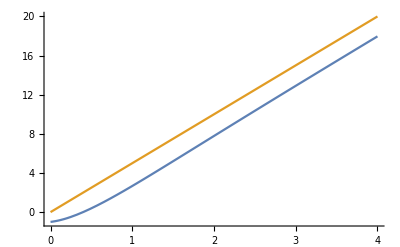

```mathematica
Plot[{Evaluate[y[x]/.s],v x},{x,0,4},PlotRange->All]
```

```mathematica
(* Problem 5: What are the intial conditions that will guarantee that the distance between you and the lead car never changes. Hint: this will only depend on the parameter v and not on k1 and k2*)

(* Problem 6: If k1=1 and  k2=3 and  v =5 and y[0]==-3, use a Mathematica plot to estimate the lowest value of y'[0] which will give an accident. You may may estimate to the nearest integer. *)
```